```mathematica
(*LQR权重矩阵*)
Subscript[Q, lqr]=DiagonalMatrix[{1,1200,50,1,12000,1}];
Subscript[R, lqr]=DiagonalMatrix[{2,10}];
Subscript[L, 0]=0.3;Subscript[Q, 0]=90;
Get["VMCsolution.m",Path->NotebookDirectory[]]
(*====================系统参数配置====================*)
(*重力加速度*)
g=9.81;
(*连杆长度*)
Subscript[L, 1]=0.150;Subscript[L, 2]=0.250;Subscript[L, 3]=Subscript[L, 2];Subscript[L, 4]=Subscript[L, 1];Subscript[L, 5]=0.108;
(*五连杆的质量分布参数*)
Subscript[l, 1]=0.064820;Subscript[l, 2]=0.126660;Subscript[l, 3]=0.147150;Subscript[l, 4]=0.064820;
Subscript[J, 1]=0.000366;Subscript[J, 2]=0.002447;Subscript[J, 3]=0.002447;Subscript[J, 4]=0.000366;
Subscript[m, 1]=0.110*2;Subscript[m, 2]=0.110*2;Subscript[m, 3]=0.165*2;Subscript[m, 4]=0.110*2;
(*机体的质量分布参数*)
Subscript[L, b]=0.009820;(*机体质心相对于关节电机轴平面的高度*)
Subscript[J, b]=0.283494;(*机体的转动惯量*)
Subscript[m, b]=11.500;(*机体的质量*)
(*驱动轮电机的质量分布参数*)
Subscript[J, wm]=0.000876;
Subscript[m, wm]=0.880*2;
(*驱动轮的质量分布参数*)
Subscript[J, w]=0.004301;(*轮子的转动惯量*)
Subscript[m, w]=0.715*2;(*驱动轮的质量*)
Subscript[R, w]=0.075;(*轮的半径*)
(*====================求解等效腿的质量分布====================*)
{Subscript[q, 0],Subscript[q, 1],Subscript[q, 2],Subscript[q, 3],Subscript[q, 4]}=VMCInverseSolution[Subscript[L, 0],Subscript[Q, 0],{Subscript[L, 1],Subscript[L, 2],Subscript[L, 3],Subscript[L, 4],Subscript[L, 5]}][[3]];
(*得各质心矢量*)
Subscript[r, 1]={Subscript[l, 1] Cos[Subscript[q, 1]],Subscript[l, 1] Sin[Subscript[q, 1]]};
Subscript[r, 2]={Subscript[L, 1] Cos[Subscript[q, 1]]+Subscript[l, 2] Cos[Subscript[q, 2]],Subscript[L, 1] Sin[Subscript[q, 1]]+Subscript[l, 2] Sin[Subscript[q, 2]]};
Subscript[r, 3]={Subscript[L, 4] Cos[Subscript[q, 4]]+Subscript[l, 3] Cos[Subscript[q, 3]]+Subscript[L, 5],Subscript[L, 4] Sin[Subscript[q, 4]]+Subscript[l, 3] Sin[Subscript[q, 3]]};
Subscript[r, 4]={Subscript[l, 4] Cos[Subscript[q, 4]]+Subscript[L, 5],Subscript[l, 4] Sin[Subscript[q, 4]]};
Subscript[r, w]={Subscript[L, 1] Cos[Subscript[q, 1]]+Subscript[L, 2] Cos[Subscript[q, 2]],Subscript[L, 1] Sin[Subscript[q, 1]]+Subscript[L, 2] Sin[Subscript[q, 2]]};
Subscript[m, l]=Subscript[m, 1]+Subscript[m, 2]+Subscript[m, 3]+Subscript[m, 4]+Subscript[m, wm];
M=Subscript[m, l]+Subscript[m, w]+Subscript[m, b];
Subscript[r, com]=Collect[Expand[Subscript[m, 1] Subscript[r, 1]+Subscript[m, 2] Subscript[r, 2]+Subscript[m, 3] Subscript[r, 3]+Subscript[m, 4] Subscript[r, 4]+Subscript[m, wm] Subscript[r, w]],{Cos[Subscript[q, 1]],Sin[Subscript[q, 1]],Cos[Subscript[q, 2]],Sin[Subscript[q, 2]],Cos[Subscript[q, 3]],Sin[Subscript[q, 3]],Cos[Subscript[q, 4]],Sin[Subscript[q, 4]]}]/Subscript[m, l];
(*求解转动惯量*)
Subscript[d, c1]=Norm[Subscript[r, 1]-Subscript[r, com]];Subscript[J, c1]=Subscript[J, 1]+Subscript[m, 1] Subscript[d, c1]^2;
Subscript[d, c2]=Norm[Subscript[r, 2]-Subscript[r, com]];Subscript[J, c2]=Subscript[J, 2]+Subscript[m, 2] Subscript[d, c2]^2;
Subscript[d, c3]=Norm[Subscript[r, 3]-Subscript[r, com]];Subscript[J, c3]=Subscript[J, 3]+Subscript[m, 3] Subscript[d, c3]^2;
Subscript[d, c4]=Norm[Subscript[r, 4]-Subscript[r, com]];Subscript[J, c4]=Subscript[J, 4]+Subscript[m, 4] Subscript[d, c4]^2;
Subscript[d, cwm]=Norm[Subscript[r, w]-Subscript[r, com]];Subscript[J, cwm]=Subscript[J, wm]+Subscript[m, wm] Subscript[d, cwm]^2;
Subscript[J, com]=Subscript[J, c1]+Subscript[J, c2]+Subscript[J, c3]+Subscript[J, c4]+Subscript[J, cwm];
(*====================腿部模型参数传递====================*)
Subscript[J, l]=Subscript[J, com];
Subscript[L, l]=Subscript[L, 0]-Norm[Subscript[r, com]-{Subscript[L, 5]/2,0}];(*腿的质心的高度*)
(*====================导入模型====================*)
θ=(Subscript[Q, 0]-90)/180*Pi;
Subscript[A, op] = Import[NotebookDirectory[]<>"A_op.wdx"];
Subscript[B, op] = Import[NotebookDirectory[]<>"B_op.wdx"];
Subscript[C, op] = DiagonalMatrix[{1,1,1,1,1,1}];
Subscript[D, op] = ConstantArray[0,{6,2}];
(*====================LQR控制====================*)
Subscript[P, lqr] = RiccatiSolve[{Subscript[A, op],Subscript[B, op]},{Subscript[Q, lqr],Subscript[R, lqr]}];(*求解黎卡提方程*)
Subscript[K, lqr] = Inverse[Subscript[R, lqr]].Subscript[B, op] ᵀ.Subscript[P, lqr]
```

{{0.325833,11.4089,31.122,5.79451,68.887,5.01954},{-0.280654,-9.84917,-40.4488,-6.53322,17.2299,2.67659}}

```mathematica
(*LQR权重矩阵*)
Subscript[Q, lqr]=DiagonalMatrix[{1,1200,50,1,12000,1}];
Subscript[R, lqr]=DiagonalMatrix[{2,10}];
(*====================系统参数配置====================*)
(*重力加速度*)
g=9.81;
(*连杆长度*)
Subscript[L, 1]=0.150;Subscript[L, 2]=0.250;Subscript[L, 3]=Subscript[L, 2];Subscript[L, 4]=Subscript[L, 1];Subscript[L, 5]=0.108;
(*五连杆的质量分布参数*)
Subscript[l, 1]=0.064820;Subscript[l, 2]=0.126660;Subscript[l, 3]=0.147150;Subscript[l, 4]=0.064820;
Subscript[J, 1]=0.000366;Subscript[J, 2]=0.002447;Subscript[J, 3]=0.002447;Subscript[J, 4]=0.000366;
Subscript[m, 1]=0.110*2;Subscript[m, 2]=0.110*2;Subscript[m, 3]=0.165*2;Subscript[m, 4]=0.110*2;
(*机体的质量分布参数*)
Subscript[L, b]=0.009820;(*机体质心相对于关节电机轴平面的高度*)
Subscript[J, b]=0.283494;(*机体的转动惯量*)
Subscript[m, b]=11.500;(*机体的质量*)
(*驱动轮电机的质量分布参数*)
Subscript[J, wm]=0.000876;
Subscript[m, wm]=0.880*2;
(*驱动轮的质量分布参数*)
Subscript[J, w]=0.004301;(*轮子的转动惯量*)
Subscript[m, w]=0.715*2;(*驱动轮的质量*)
Subscript[R, w]=0.075;(*轮的半径*)
(*限位*)
upLimit=-23.41;(*上限位*)
downLimit=67.89;(*下限位*)
(*电机半径--画图*)
Subscript[R, jm]=0.045;(*GO8010*)
Subscript[R, wm]=0.0675;(*MF9025*)
(*Save[NotebookDirectory[]<>"\\VMCsolution.m",VMCForwardSolution,VMCInverseSolution];*)
Get["VMCsolution.m",Path->NotebookDirectory[]]
SystemCalcu[L0_,Q0_]:=(
Module[{},
Subscript[L, 0]=L0;
{Subscript[q, 0],Subscript[q, 1],Subscript[q, 2],Subscript[q, 3],Subscript[q, 4]}=VMCInverseSolution[L0,Q0,{Subscript[L, 1],Subscript[L, 2],Subscript[L, 3],Subscript[L, 4],Subscript[L, 5]}][[3]];
(*====================求解等效腿的质量分布====================*)
(*得各质心矢量*)
Subscript[r, 1]={Subscript[l, 1] Cos[Subscript[q, 1]],Subscript[l, 1] Sin[Subscript[q, 1]]};
Subscript[r, 2]={Subscript[L, 1] Cos[Subscript[q, 1]]+Subscript[l, 2] Cos[Subscript[q, 2]],Subscript[L, 1] Sin[Subscript[q, 1]]+Subscript[l, 2] Sin[Subscript[q, 2]]};
Subscript[r, 3]={Subscript[L, 4] Cos[Subscript[q, 4]]+Subscript[l, 3] Cos[Subscript[q, 3]]+Subscript[L, 5],Subscript[L, 4] Sin[Subscript[q, 4]]+Subscript[l, 3] Sin[Subscript[q, 3]]};
Subscript[r, 4]={Subscript[l, 4] Cos[Subscript[q, 4]]+Subscript[L, 5],Subscript[l, 4] Sin[Subscript[q, 4]]};
Subscript[r, w]={Subscript[L, 1] Cos[Subscript[q, 1]]+Subscript[L, 2] Cos[Subscript[q, 2]],Subscript[L, 1] Sin[Subscript[q, 1]]+Subscript[L, 2] Sin[Subscript[q, 2]]};
Subscript[m, l]=Subscript[m, 1]+Subscript[m, 2]+Subscript[m, 3]+Subscript[m, 4]+Subscript[m, wm];
M=Subscript[m, l]+Subscript[m, w]+Subscript[m, b];
Subscript[r, com]=Collect[Expand[Subscript[m, 1] Subscript[r, 1]+Subscript[m, 2] Subscript[r, 2]+Subscript[m, 3] Subscript[r, 3]+Subscript[m, 4] Subscript[r, 4]+Subscript[m, wm] Subscript[r, w]],{Cos[Subscript[q, 1]],Sin[Subscript[q, 1]],Cos[Subscript[q, 2]],Sin[Subscript[q, 2]],Cos[Subscript[q, 3]],Sin[Subscript[q, 3]],Cos[Subscript[q, 4]],Sin[Subscript[q, 4]]}]/Subscript[m, l];
(*求解转动惯量*)
Subscript[d, c1]=Norm[Subscript[r, 1]-Subscript[r, com]];Subscript[J, c1]=Subscript[J, 1]+Subscript[m, 1] Subscript[d, c1]^2;
Subscript[d, c2]=Norm[Subscript[r, 2]-Subscript[r, com]];Subscript[J, c2]=Subscript[J, 2]+Subscript[m, 2] Subscript[d, c2]^2;
Subscript[d, c3]=Norm[Subscript[r, 3]-Subscript[r, com]];Subscript[J, c3]=Subscript[J, 3]+Subscript[m, 3] Subscript[d, c3]^2;
Subscript[d, c4]=Norm[Subscript[r, 4]-Subscript[r, com]];Subscript[J, c4]=Subscript[J, 4]+Subscript[m, 4] Subscript[d, c4]^2;
Subscript[d, cwm]=Norm[Subscript[r, w]-Subscript[r, com]];Subscript[J, cwm]=Subscript[J, wm]+Subscript[m, wm] Subscript[d, cwm]^2;
Subscript[J, com]=Subscript[J, c1]+Subscript[J, c2]+Subscript[J, c3]+Subscript[J, c4]+Subscript[J, cwm];
(*====================腿部模型参数传递====================*)
Subscript[J, l]=Subscript[J, com];
Subscript[L, l]=Subscript[L, 0]-Norm[Subscript[r, com]-{Subscript[L, 5]/2,0}];(*腿的质心的高度*)
(*====================导入模型====================*)
θ=(Subscript[Q, 0]-90)/180*Pi;
Subscript[A, op] = Import[NotebookDirectory[]<>"A_op.wdx"];
Subscript[B, op] = Import[NotebookDirectory[]<>"B_op.wdx"];
Subscript[C, op] = DiagonalMatrix[{1,1,1,1,1,1}];
Subscript[D, op] = ConstantArray[0,{6,2}];
(*====================LQR控制====================*)
Subscript[P, lqr] = RiccatiSolve[{Subscript[A, op],Subscript[B, op]},{Subscript[Q, lqr],Subscript[R, lqr]}];(*求解黎卡提方程*)
Subscript[K, lqr] = Inverse[Subscript[R, lqr]].Subscript[B, op] ᵀ.Subscript[P, lqr];
Return[Subscript[K, lqr]];
];
);
Manipulate[SystemCalcu[L0,Q0],{{L0,0.2},0.1,0.4},{{Q0,90},180,0}](*显示具体数值*)
```

{0.797097-2.15505 x+1.83349 x^2+0.370208 x^3,27.8285-75.0203 x+63.5743 x^2+13.2001 x^3,18.0587+186.706 x-705.858 x^2+761.812 x^3,1.63162+33.6432 x-91.428 x^2+85.1404 x^3,2.88994+478.703 x-1173.57 x^2+1038. x^3,-3.89182+63.0659 x-150.771 x^2+131.948 x^3,-0.0267526-1.84735 x+4.54192 x^2-4.0202 x^3,-0.949843-64.5161 x+158.061 x^2-139.728 x^3,-0.141779-188.896 x+214.882 x^2-110.629 x^3,0.114695-16.1936 x-31.1215 x^2+37.3942 x^3,40.7147-106.452 x+87.1307 x^2+22.1354 x^3,5.19391-10.7512 x+6.66148 x^2+3.99882 x^3}

{{0.797097,-2.15505,1.83349,0.370208},{27.8285,-75.0203,63.5743,13.2001},{18.0587,186.706,-705.858,761.812},{1.63162,33.6432,-91.428,85.1404},{2.88994,478.703,-1173.57,1038.},{-3.89182,63.0659,-150.771,131.948},{-0.0267526,-1.84735,4.54192,-4.0202},{-0.949843,-64.5161,158.061,-139.728},{-0.141779,-188.896,214.882,-110.629},{0.114695,-16.1936,-31.1215,37.3942},{40.7147,-106.452,87.1307,22.1354},{5.19391,-10.7512,6.66148,3.99882}}

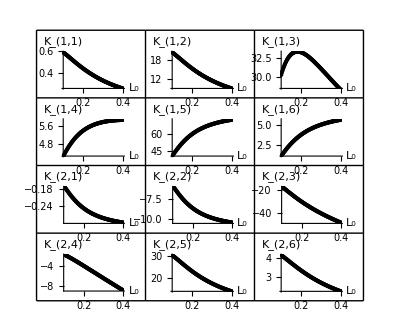

```mathematica
(*LQR权重矩阵*)
Subscript[Q, lqr]=DiagonalMatrix[{1,1200,50,1,12000,1}];
Subscript[R, lqr]=DiagonalMatrix[{2,10}];
Subscript[L, 0]=0.3;Subscript[Q, 0]=90;
Get["VMCsolution.m",Path->NotebookDirectory[]]
(*=============================================系统参数配置=============================================*)
(*重力加速度*)
g=9.81;
(*连杆长度*)
Subscript[L, 1]=0.150;Subscript[L, 2]=0.250;Subscript[L, 3]=Subscript[L, 2];Subscript[L, 4]=Subscript[L, 1];Subscript[L, 5]=0.108;
(*五连杆的质量分布参数*)
Subscript[l, 1]=0.064820;Subscript[l, 2]=0.126660;Subscript[l, 3]=0.147150;Subscript[l, 4]=0.064820;
Subscript[J, 1]=0.000366;Subscript[J, 2]=0.002447;Subscript[J, 3]=0.002447;Subscript[J, 4]=0.000366;
Subscript[m, 1]=0.110*2;Subscript[m, 2]=0.110*2;Subscript[m, 3]=0.165*2;Subscript[m, 4]=0.110*2;
(*机体的质量分布参数*)
Subscript[L, b]=0.009820;(*机体质心相对于关节电机轴平面的高度*)
Subscript[J, b]=0.283494;(*机体的转动惯量*)
Subscript[m, b]=11.500;(*机体的质量*)
(*驱动轮电机的质量分布参数*)
Subscript[J, wm]=0.000876;
Subscript[m, wm]=0.880*2;
(*驱动轮的质量分布参数*)
Subscript[J, w]=0.004301;(*轮子的转动惯量*)
Subscript[m, w]=0.715*2;(*驱动轮的质量*)
Subscript[R, w]=0.075;(*轮的半径*)
(*=============================================开始循环迭代============================================*)
sampleNum=101;(*循环次数*)
paramNum=12;(*变量个数*)
Kt=Array[0,{sampleNum}];
Lt=Array[0,{sampleNum}];
Do[
(*输入量控制*)
Subscript[L, 0]=0.10+0.3*(cnt)/sampleNum;
Subscript[Q, 0]=90;
(*=========================================求解等效腿的质量分布====================================*)
{Subscript[q, 0],Subscript[q, 1],Subscript[q, 2],Subscript[q, 3],Subscript[q, 4]}=VMCInverseSolution[Subscript[L, 0],Subscript[Q, 0],{Subscript[L, 1],Subscript[L, 2],Subscript[L, 3],Subscript[L, 4],Subscript[L, 5]}][[3]];
(*得各质心矢量*)
Subscript[r, 1]={Subscript[l, 1] Cos[Subscript[q, 1]],Subscript[l, 1] Sin[Subscript[q, 1]]};
Subscript[r, 2]={Subscript[L, 1] Cos[Subscript[q, 1]]+Subscript[l, 2] Cos[Subscript[q, 2]],Subscript[L, 1] Sin[Subscript[q, 1]]+Subscript[l, 2] Sin[Subscript[q, 2]]};
Subscript[r, 3]={Subscript[L, 4] Cos[Subscript[q, 4]]+Subscript[l, 3] Cos[Subscript[q, 3]]+Subscript[L, 5],Subscript[L, 4] Sin[Subscript[q, 4]]+Subscript[l, 3] Sin[Subscript[q, 3]]};
Subscript[r, 4]={Subscript[l, 4] Cos[Subscript[q, 4]]+Subscript[L, 5],Subscript[l, 4] Sin[Subscript[q, 4]]};
Subscript[r, w]={Subscript[L, 1] Cos[Subscript[q, 1]]+Subscript[L, 2] Cos[Subscript[q, 2]],Subscript[L, 1] Sin[Subscript[q, 1]]+Subscript[L, 2] Sin[Subscript[q, 2]]};
Subscript[m, l]=Subscript[m, 1]+Subscript[m, 2]+Subscript[m, 3]+Subscript[m, 4]+Subscript[m, wm];
M=Subscript[m, l]+Subscript[m, w]+Subscript[m, b];
Subscript[r, com]=Collect[Expand[Subscript[m, 1] Subscript[r, 1]+Subscript[m, 2] Subscript[r, 2]+Subscript[m, 3] Subscript[r, 3]+Subscript[m, 4] Subscript[r, 4]+Subscript[m, wm] Subscript[r, w]],{Cos[Subscript[q, 1]],Sin[Subscript[q, 1]],Cos[Subscript[q, 2]],Sin[Subscript[q, 2]],Cos[Subscript[q, 3]],Sin[Subscript[q, 3]],Cos[Subscript[q, 4]],Sin[Subscript[q, 4]]}]/Subscript[m, l];
(*求解转动惯量*)
Subscript[d, c1]=Norm[Subscript[r, 1]-Subscript[r, com]];Subscript[J, c1]=Subscript[J, 1]+Subscript[m, 1] Subscript[d, c1]^2;
Subscript[d, c2]=Norm[Subscript[r, 2]-Subscript[r, com]];Subscript[J, c2]=Subscript[J, 2]+Subscript[m, 2] Subscript[d, c2]^2;
Subscript[d, c3]=Norm[Subscript[r, 3]-Subscript[r, com]];Subscript[J, c3]=Subscript[J, 3]+Subscript[m, 3] Subscript[d, c3]^2;
Subscript[d, c4]=Norm[Subscript[r, 4]-Subscript[r, com]];Subscript[J, c4]=Subscript[J, 4]+Subscript[m, 4] Subscript[d, c4]^2;
Subscript[d, cwm]=Norm[Subscript[r, w]-Subscript[r, com]];Subscript[J, cwm]=Subscript[J, wm]+Subscript[m, wm] Subscript[d, cwm]^2;
Subscript[J, com]=Subscript[J, c1]+Subscript[J, c2]+Subscript[J, c3]+Subscript[J, c4]+Subscript[J, cwm];
(*============================================腿部模型参数传递====================================*)
Subscript[J, l]=Subscript[J, com];
Subscript[L, l]=Subscript[L, 0]-Norm[Subscript[r, com]-{Subscript[L, 5]/2,0}];(*腿的质心的高度*)
(*============================================导入模型============================================*)
θ=(Subscript[Q, 0]-90)/180*Pi;
Subscript[A, op] = Import[NotebookDirectory[]<>"A_op.wdx"];
Subscript[B, op] = Import[NotebookDirectory[]<>"B_op.wdx"];
Subscript[C, op] = DiagonalMatrix[{1,1,1,1,1,1}];
Subscript[D, op] = ConstantArray[0,{6,2}];
(*============================================LQR控制============================================*)
Subscript[P, lqr] = RiccatiSolve[{Subscript[A, op],Subscript[B, op]},{Subscript[Q, lqr],Subscript[R, lqr]}];(*求解黎卡提方程*)
Subscript[K, lqr] = Inverse[Subscript[R, lqr]].Subscript[B, op] ᵀ.Subscript[P, lqr];
(*============================================数据记录===========================================*)
Kt[[cnt]] = Subscript[K, lqr];
Lt[[cnt]] = Subscript[L, 0];
,{cnt,sampleNum}];
(*============================================多项式拟合============================================*)
(*提取同一参数在不同条件下的值*)
kArray=Array[0,{paramNum}];Do[Do[kArray[[(i-1)*6+j]]=Kt[[All,i,j]],{j,6}],{i,2}];	
(*将条件值与参数值配对*)
Kxy=Array[0,{paramNum,sampleNum}];
Do[Do[Kxy[[i,j]]={Lt[[j]],kArray[[i,j]]},{j,sampleNum}],{i,paramNum}];	
(*分别对各个参数进行多项式拟合*)
Kpoly = Array[0, {paramNum}];
Do[Kpoly[[i]]= Fit[Kxy[[i]],{1,x,x^2,x^3},x],{i,paramNum}];
Kpoly
(*将多项式系数整合成一个矩阵*)
kPolyMatrix = Array[0,{12}];
Do[kPolyMatrix[[i]]=CoefficientList[Kpoly[[i]],x],{i,paramNum}];
(*多项式拟合曲线*)
KT = Array[0, {paramNum}];
Do[KT[[plotcnt]] = Plot[Kpoly[[plotcnt]], {x, Lt[[1]], Lt[[sampleNum]]}, Epilog->Point[Kxy[[plotcnt]]],Axes->{True,True}, AxesLabel->{"L_0", Subscript[K, 1,plotcnt]}],{plotcnt, 1, 6}];
Do[KT[[plotcnt]] = Plot[Kpoly[[plotcnt]], {x, Lt[[1]], Lt[[sampleNum]]}, Epilog->Point[Kxy[[plotcnt]]],Axes->{True,True}, AxesLabel->{"L_0", Subscript[K, 2,plotcnt-6]}],{plotcnt, 7, 12}];
KL0Graph = GraphicsGrid[{{KT [[1]],KT [[2]],KT [[3]]},{KT [[4]],KT [[5]],KT [[6]]},
	{KT [[7]],KT [[8]],KT [[9]]},{KT [[10]],KT [[11]],KT [[12]]}}, Frame->All,ImageSize->Full];
(*============================================数据输出===========================================*)
Print[kPolyMatrix];(*拟合多项式升幂排列*)
Show[KL0Graph](*多项式拟合曲线图*)
```